## test for homogeneous traveltime

```mathematica
Clear["Global`*"]
```

```mathematica
param={eta->0.2,t0->1,vn->2}
```

{eta→0.2,t0→1,vn→2}

```mathematica
Xp=((1+2 eta) p t0 vn^2 √(((1+2 eta) (-1+2 eta (-1+(1+2 eta) p^2 vn^2)))/(-1+(1+2 eta) p^2 vn^2)))/((1-2 eta (-1+(1+2 eta) p^2 vn^2))^2);
```

```mathematica
TT1=t0+(t0 (-1+√(1+((1+8 eta) x^2)/(t0^2 vn^2))))/(1+8 eta);
TT2=Sqrt[t0^2+x^2/vn^2-(2 eta x^4)/(t0^2 vn^4 (1+((1+2 eta) x^2)/(t0^2 vn^2)))];
TT22=(24 t0^10 vn^10+2 (51+104 eta) t0^8 vn^8 x^2+56 (3+8 eta) t0^6 vn^6 x^4+4 (33+69 eta-16 eta^2) t0^4 vn^4 x^6+8 (6+5 eta+2 eta^2) t0^2 vn^2 x^8+(6+4 eta-eta^2) x^10)/(2 vn (t0^2 vn^2+x^2)^(3/2) (12 t0^6 vn^6+(27+104 eta) t0^4 vn^4 x^2+2 (9+14 eta) t0^2 vn^2 x^4+(3+5 eta) x^6));
TT3=√(t0^2+x^2/vn^2-(4 eta x^4)/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) *t0^2*x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))));
```

```mathematica
Simplify[TT3,t0>0]
```

√(t0^2+x^2/vn^2-(4 eta x^4)/(vn^4 (t0^2+((1+8 eta+8 eta^2) x^2)/((1+2 eta) vn^2)+√(t0^4+(2 (1+8 eta+8 eta^2) t0^2 x^2)/((1+2 eta) vn^2)+x^4/((1+2 eta)^2 vn^4)))))

```mathematica
TTe=√(t0^2 (√(((1+2 eta) (-1+(1+2 eta) p^2 vn^2))/(-1+2 eta (-1+(1+2 eta) p^2 vn^2)))+((1+2 eta) p^2 vn^2 √(((1+2 eta) (-1+2 eta (-1+(1+2 eta) p^2 vn^2)))/(-1+(1+2 eta) p^2 vn^2)))/((1-2 eta (-1+(1+2 eta) p^2 vn^2))^2))^2);
```

```mathematica
pp1=Abs[(TTe-TT1)]*100/TTe/.x->Xp;
pp2=Abs[(TTe-TT2)]*100/TTe/.x->Xp;
pp22=Abs[(TTe-TT22)]*100/TTe/.x->Xp;
pp3=Abs[(TTe-TT3)]*100/TTe/.x->Xp;
```

```mathematica
YY=x/(t0*vn)/.x->Xp;
```

```mathematica
{a00=ParametricPlot[{YY/.param,pp1/.param},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,1.1}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"shifted hyperbola"},Right]],
a01=ParametricPlot[{YY/.param,pp2/.param},{p,0,0.9},PlotStyle->{Directive[Dotted,Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,1.1}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"rational"},Right]],a012=ParametricPlot[{YY/.param,pp22/.param},{p,0,0.9},PlotStyle->{Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,1.1}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"shanks transform"},Right]]};
```

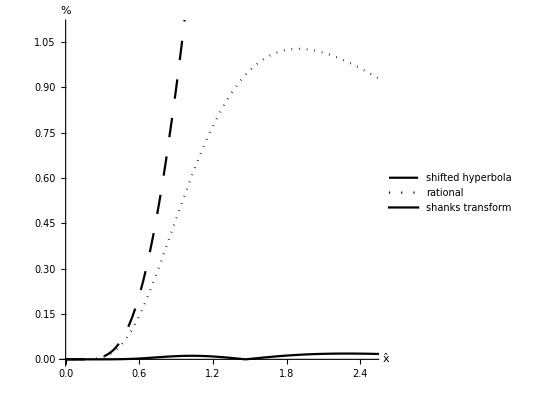

```mathematica
Show[a00,a01,a012]
```

```mathematica
GS1=((1/x)*D[TT1,x]*(D[TT1,{x,2}]))^(-1/2);
```

```mathematica
GS2=Simplify[((1/x)*D[TT2,x]*(D[TT2,{x,2}]))^(-1/2),t0>0&&vn>0]
```

```mathematica
((1/x)*D[TT2,x]*(D[TT2,{x,2}]))^(-1/2)
```

(√2)/(√((((2 x)/vn^2+(4 eta (1+2 eta) x^5)/(t0^4 vn^6 (1+((1+2 eta) x^2)/(t0^2 vn^2))^2)-(8 eta x^3)/(t0^2 vn^4 (1+((1+2 eta) x^2)/(t0^2 vn^2)))) (-(((2 x)/vn^2+(4 eta (1+2 eta) x^5)/(t0^4 vn^6 (1+((1+2 eta) x^2)/(t0^2 vn^2))^2)-(8 eta x^3)/(t0^2 vn^4 (1+((1+2 eta) x^2)/(t0^2 vn^2))))^2)/(4 (t0^2+x^2/vn^2-(2 eta x^4)/(t0^2 vn^4 (1+((1+2 eta) x^2)/(t0^2 vn^2))))^(3/2))+(2/vn^2-(16 eta (1+2 eta)^2 x^6)/(t0^6 vn^8 (1+((1+2 eta) x^2)/(t0^2 vn^2))^3)+(36 eta (1+2 eta) x^4)/(t0^4 vn^6 (1+((1+2 eta) x^2)/(t0^2 vn^2))^2)-(24 eta x^2)/(t0^2 vn^4 (1+((1+2 eta) x^2)/(t0^2 vn^2))))/(2 √(t0^2+x^2/vn^2-(2 eta x^4)/(t0^2 vn^4 (1+((1+2 eta) x^2)/(t0^2 vn^2)))))))/(x √(t0^2+x^2/vn^2-(2 eta x^4)/(t0^2 vn^4 (1+((1+2 eta) x^2)/(t0^2 vn^2)))))))

```mathematica
GS3=((1/x)*D[TT3,x]*(D[TT3,{x,2}]))^(-1/2);
```

```mathematica
GS22=((1/x)*D[TT22,x]*(D[TT22,{x,2}]))^(-1/2);
```

```mathematica
GRP=t0 vn^2+(-(-1-8 eta)/t0)*x^2+(-(9 (eta+4 eta^2))/(t0^3 vn^2))*x^4/(1+(-(9 eta (1+4 eta))/((-1-8 eta+1/(√(1+2 eta))) t0^2 vn^2))*x^2);
```

```mathematica
GSe=Sqrt[(Xp/p)*D[Xp,p]];
```

```mathematica
bb1=Abs[(GSe-GS1)]*100/GSe/.x->Xp;
bb2=Abs[(GSe-GS2)]*100/GSe/.x->Xp;
bb22=Abs[(GSe-GS22)]*100/GSe/.x->Xp;
bb3=Abs[(GSe-GS3)]*100/GSe/.x->Xp;
```

```mathematica
{b00=ParametricPlot[{YY/.param,bb1/.param},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,8}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"shifted hyperbola"},Right]],
b01=ParametricPlot[{YY/.param,bb2/.param},{p,0,0.9},PlotStyle->{Directive[Dotted,Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,8}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"rational"},Right]],b012=ParametricPlot[{YY/.param,bb22/.param},{p,0,0.9},PlotStyle->{Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,2.5},{0,8}},AxesLabel->{Style["x̂",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"shanks transform"},Right]]};
```

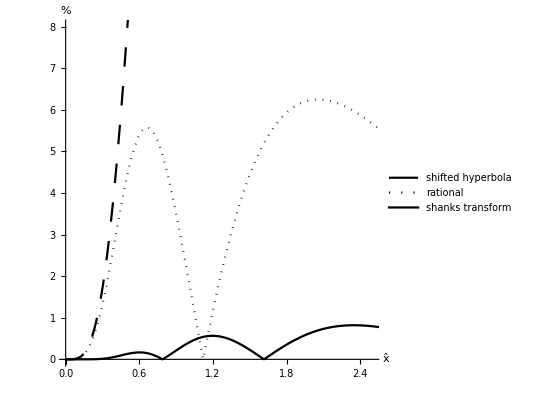

```mathematica
Show[b00,b01,b012]
```